# Monte Carlo P Values with Gaussian

https://www.youtube.com/watch?v=8qrfSh07rT0

The Student T distribution is perfectly symmetric. The mean is equal to the median. https://arxiv.org/pdf/1603.07532.pdf 

There is more from the video that I did not fill in since he had an analytical function that he has worked out in the prior. It was a big mess.

```mathematica
dist = NormalDistribution[.5,1];
```

Generate the mean. Note that this value will follow a Student-T distribution.

```mathematica
ta=Table[smpl = RandomVariate[dist, 30]; Mean[smpl]/StandardDeviation[smpl] Sqrt[30],{10^4}];
{Mean[ta]}
```

{2.7945}

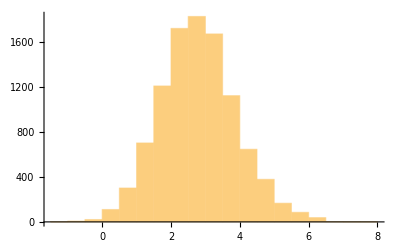

```mathematica
Histogram[ta]
```

Probability of those exceeding this function.

```mathematica
ta2=SurvivalFunction[StudentTDistribution[0,1,29],ta];
```

```mathematica
Mean[ta2]
```

0.0297329

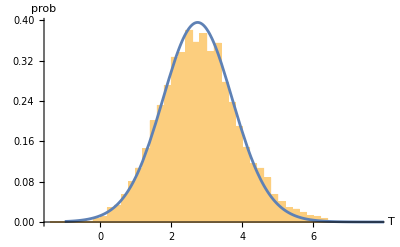

```mathematica
Show[Histogram[ta,50,"PDF"],Plot[PDF[StudentTDistribution[0.5Sqrt[30],1,29],x],{x,-1,8}],AxesLabel->{"T",prob}]
```

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

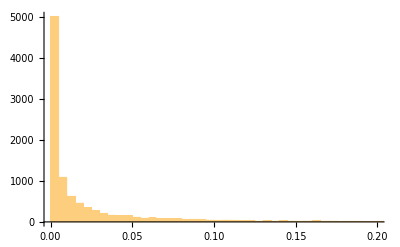

```mathematica
hist = Histogram[ta2,"PDF",PlotRange->{{0,0.2}, Automatic}]
```

```mathematica
med = Median[ta2]
```

0.00497903

```mathematica
Mean[ta2]
```

0.0297329

There is based on upper bound and lower bounds that you can seeing how people get the p-values.